```mathematica
Remove["Global`*"]
```

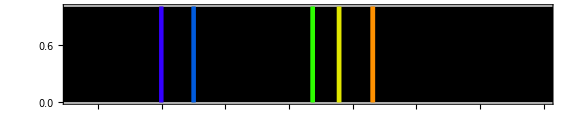

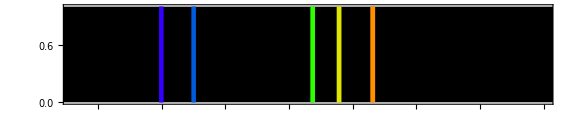

```mathematica
spectrum[list_List]:=Graphics[{Thickness[0.005],ColorData["VisibleSpectrum"][#],Line[{{#,0},{#,1}}]}&/@list,PlotRange->{{380,750},{0,1}},PlotRangePadding->None,ImagePadding->All,AspectRatio->1/5,ImageSize->Large,Axes->None,Frame->{True,False,True,False},Prolog->Rectangle[{0,0},{1000,1}]]
(* Wavelengths in nanometers *)
Ne={448.809226,533.07775,540.05617,565.65664,576.44188,580.44496,585.24878,588.1895,594.48342,609.61631,612.84499,626.6495,633.44278,638.29917,640.2246,650.65281,667.82764,703.24131,724.51666,743.8899,748.88712};
NaData={4747.859,4751.709,4494.184,4497.555,5890.065,5896.069,5682.539,5688.15,6154.325,6160.887}/10;
NaActual={4494.266,4497.724,4748.016,4751.891,5682.657,5688.224,5889.953,5895.923,6154.229,6160.760}/10;

(*spectrum[Ne]*)
spectrum[NaData]
spectrum[NaActual]
(*spectrum[Table[i,{i,400,750,0.01}]]*)
```